```mathematica
s
```

```mathematica
Select[
```

Once the expressions are acquired

```mathematica
SetAttributes[Timer,{HoldAll}];
Timer[expr_] :=
Block[
{result},
ClearSystemCache[];
result = AbsoluteTiming[expr];CellPrint[
   TextCell[
    GeneralUtilities`TimeString[First[result]],
    "Text",
    FontColor -> Darker@Red
    ]
   ];
  Last[result]
]
```

## Function to count Heads

```mathematica
bannedSymbols = {"Symbol", "Integer", "Times", "Rule", "Legended", "Graphics", "Plus", "Inactive", "HoldComplete", "List", "Power", "Set"}; 
FDistributionSLOW[input___] := KeyDrop[   (* The input needs to be an Inactive/HoldComplete list of functions *)
Counts[
Select[ToString /@ Level[input,{0,Infinity}, Heads->True], ContainsAny[Names["System`*"], {#}] &]
], bannedSymbols
] 

(* WWAAAYYYY faster with DeleteCases! *)
(* Cases[ToString /@ Level[input,{0,Infinity}, Heads->True], exceptions] *) (* ToString is no tthe best here *)
exceptions =  Alternatives @@ Names["System`*"];
FDistribution[input___, current_String] := KeyDrop[   (* The input needs to be an Inactive/HoldComplete list of functions *)
	Counts[
		Cases[input, s_Symbol /; MatchQ[SymbolName[Unevaluated[s]], exceptions]:> SymbolName[Unevaluated[s]], {0, Infinity}, Heads->True] 
	], Append[bannedSymbols, current]
] 

FDistribution[input___] := FDistribution[input, ""]
```

## Convert documentation to input

```mathematica
FConvertDoc[doc_List] := (doc // ToBoxes // MakeExpression) /. ExpressionCell[a_,__] :>a
FConvertDoc[function_String, level_Integer]:= FConvertDoc[Flatten @ WolframLanguageData[function, "DocumentationExampleInputs"][[level, 2]]]
```

## On a lot of things

```mathematica
FFrequencyList[functions_List, level_Integer] := Map[ 
	<| # -> FDistribution[FConvertDoc[#,level], # ] |> &, functions
]
```

## Graphs and other funny jokes you can tell yourself

```mathematica
<< "Data/BasicExamplesFixed.mx";
<< "Data/FunctionList.mx";
```

```mathematica
keys = Keys @ basicExamples;
values = Values @ ParallelMap[Lookup[#, keys, 0] & ,basicExamples];
sarray = SparseArray[values];
```

```mathematica
graph = AdjacencyGraph[keys, values, DirectedEdges->False]
```

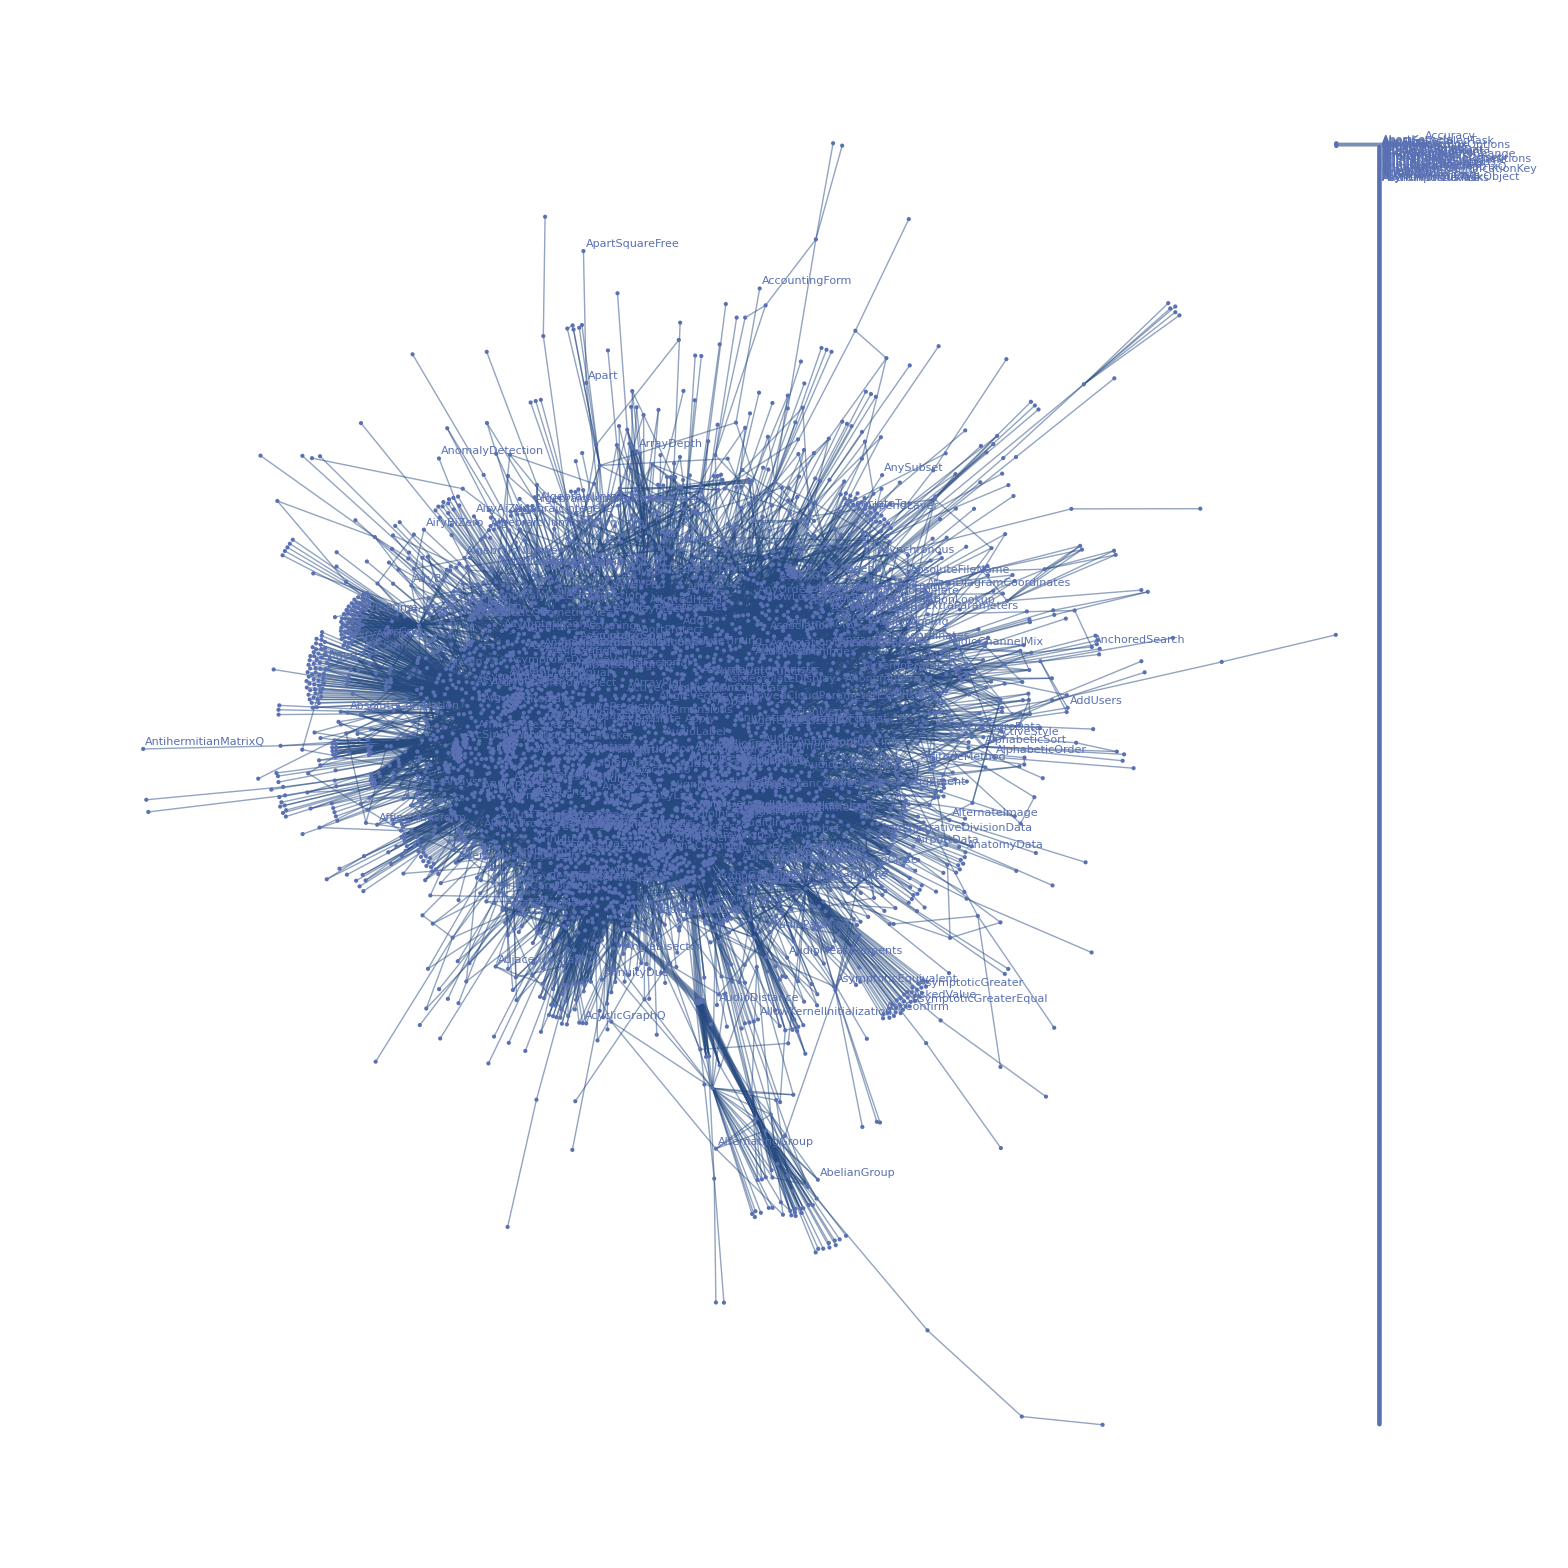

```mathematica
GraphPlot[graph, VertexLabels->Automatic]
```

One way of doing things, associate a degree to a weight, the more connection there is to it the more chance there is to be used with.

Some problems with this way of doing things. Using the inverse works too, but it leads to some unknown functions being in the most frequently used with of a function that is way more known.

```mathematica
weight = SortBy[AssociationThread[Keys @ basicExamples, ((VertexDegree[graph]+1)/Max[VertexDegree[graph]+1])], Plus] (* +1 for preventing division by 0 *)
```

<|AbortKernels→1/613,AbortScheduledTask→1/613,AbsArg→1/613,Absolute→1/613,ActionDelay→1/613,ActionMenuBox→1/613,ActionMenuBoxOptions→1/613,Active→1/613,ActiveItem→1/613,AddOnHelpPath→1/613,AlgebraicRules→1/613,AlgebraicRulesData→1/613,AlignmentMarker→1/613,AllowAdultContent→1/613,AllowIncomplete→1/613,AllowScriptLevelChange→1/613,AmbientLight→1/613,Analytic→1/613,AnatomyForm→1/613,AngleBracket→1/613,6139,Axis→186/613,Disk→188/613,Map→190/613,Entity→194/613,Blank→198/613,Filling→211/613,Graphics3D→212/613,Image→243/613,Pi→268/613,PlotRange→269/613,Association→271/613,ColorSpace→271/613,Interleaving→271/613,ImageSize→295/613,Graphics→297/613,Sin→329/613,Automatic→521/613,Table→521/613,All→538/613,Plot→1|>
 |  |  |  |

```mathematica
test = basicExamples;
test[["Sin"]]
```

<|Pi→2,Degree→1,Plot→1,Series→1|>

```mathematica
Map[test[["Sin"]][[#]] * weight[[#]] &, Keys @ test[["Sin"]]] // N
```

{0.874388,0.0489396,1.,0.213703}

```mathematica
tkey = "ColorBalance";
```

```mathematica
test[[tkey]]

maxflow = Map[FindMaximumFlow[graph, tkey, #] &, Keys @ test[[tkey]]]
weighted = Map[test[[tkey]][[#]] * weight[[#]] &, Keys @ test[[tkey]]] // N
```

<|Image→1,ColorSpace→1,ImageSize→1,All→1,Interleaving→1,MetaInformation→1|>

{6,6,6,6,6,6}

{0.396411,0.442088,0.48124,0.877651,0.442088,0.0815661}

```mathematica
AssociationThread[Keys@basicExamples[[tkey]],maxflow * weighted]//ReverseSort//Dataset
```

Dataset[<>]

```mathematica
FindMaximumFlow[graph, "Plot", "Sin"]
```

326

Giulio stuff

```mathematica
keys = Keys @ joinedBasicExamples  ;
```

```mathematica
joinedBasicExamples = Join @@  basicExamples ;
```

```mathematica
values = Values @ ParallelMap[Lookup[#, keys, 0]&, joinedBasicExamples];
```

```mathematica
Dimensions[values]
```

{6177,6177}

```mathematica
fullgraph = AdjacencyGraph[keys, values, DirectedEdges->False]
```

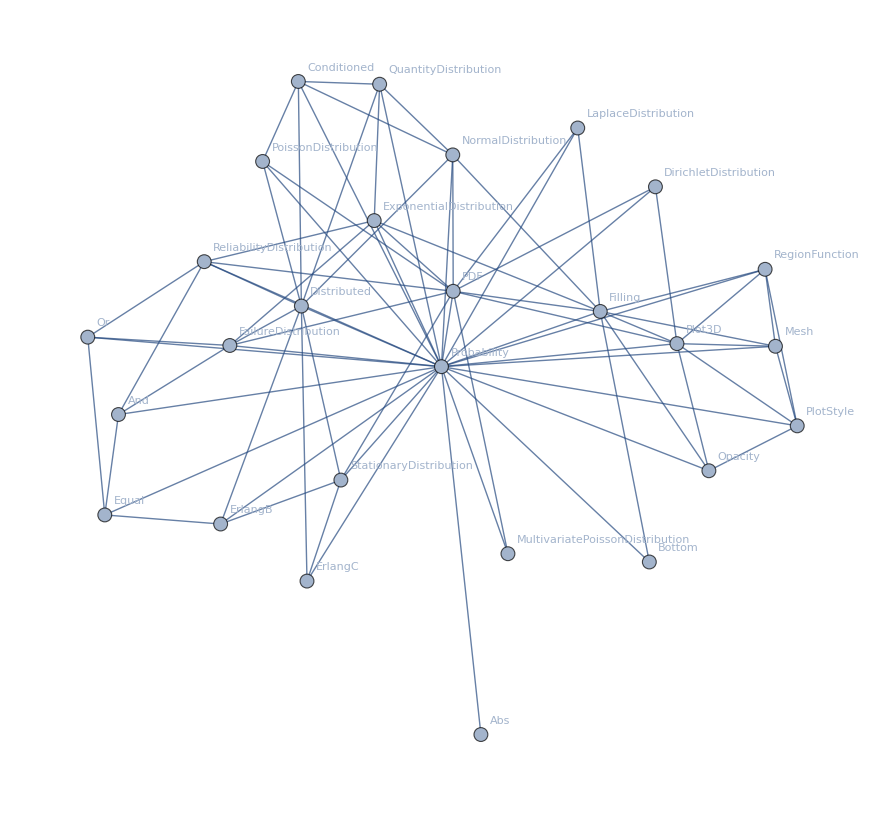

```mathematica
Subgraph[fullgraph, VertexComponent[fullgraph, "Probability", 1], VertexLabels->Automatic]
```

```mathematica
Subgraph[fullgraph, VertexComponent[fullgraph, selectionTest, 1], VertexLabels->labels];
```

```mathematica
FindShortestPath[fullgraph, "URLDownload", "Plot"]
```

{URLDownload,Automatic,Plot}

```mathematica
indentingNewLine="
";
```

```mathematica
fixes={indentingNewLine->Nothing};
```

```mathematica
selectionTest = Flatten @ Position[keys, "Probability" ]
```

{4399}

```mathematica
labels = Thread[Range[Length[keys]] -> keys];
```

```mathematica
VertexComponent[fullgraph, selectionTest, 1]
```

{4399,957,1509,1745,1746,1883,4463,4632,5248}

```mathematica
MeanDegreeConnectivity[fullgraph]// N
keys[[2]]
```

```mathematica
WolframLanguageData["Plot", "Options"]// Keys
```

{AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,BaselinePosition,BaseStyle,ClippingStyle,ColorFunction,ColorFunctionScaling,ContentSelectable,CoordinatesToolOptions,DisplayFunction,Epilog,EvaluationMonitor,Exclusions,ExclusionsStyle,Filling,FillingStyle,FormatType,Frame,FrameLabel,FrameStyle,FrameTicks,FrameTicksStyle,GridLines,GridLinesStyle,ImageMargins,ImagePadding,ImageSize,LabelingSize,LabelStyle,MaxRecursion,Mesh,MeshFunctions,MeshShading,MeshStyle,Method,PerformanceGoal,PlotLabel,PlotLabels,PlotLegends,PlotPoints,PlotRange,PlotRangeClipping,PlotRangePadding,PlotRegion,PlotStyle,PlotTheme,PreserveImageOptions,Prolog,RegionFunction,RotateLabel,ScalingFunctions,TargetUnits,Ticks,TicksStyle,WorkingPrecision}

```mathematica
test
```

<|AASTriangle→<|Pi→8,Graphics→5,EdgeForm→3,Thick→2,Dashed→2,Directive→1,Area→1,RegionCentroid→1|>,AbelianGroup→<|GroupOrder→1,GroupGenerators→1,GroupElements→1|>,Abort→<|Print→2,SetDelayed→1,Pattern→3,Blank→3,FixedPoint→1,If→3,Greater→3,Abs→1,Exp→1,NDSolve→2,Equal→4,Derivative→2,Sqrt→2|>,AbortKernels→<||>,AbortProtect→<|Abort→1,Print→2,TimeConstrained→2,Do→2,N→2,Table→1|>,6170,ZoomCenter→<|ExampleData→1,DynamicImage→2,Center→1,Top→1|>,ZoomFactor→<|ExampleData→1,DynamicImage→4|>,ZTest→<|SeedRandom→4,RandomVariate→6,NormalDistribution→3,SmoothHistogram→2,Mean→2,Sqrt→2,MultinormalDistribution→3,IdentityMatrix→5|>,ZTransform→<|InverseZTransform→2|>|>
 |  |  |  |